```mathematica
(35.4+48.6)/28
```

3.

```mathematica
17.2*4.35
```

74.82

```mathematica
4.3^3
```

79.507

```mathematica
326^(1/5)
```

326^(1/5)

```mathematica
$MinMachineNumber
```

2.22507×10^-308

```mathematica
$MaxMachineNumber
```

1.79769×10^308

```mathematica
x:=123^2/768
```

```mathematica
IntegerPart[x]
FractionalPart[x]
```

19

179/256

```mathematica
y:=Pi*E^(-2)
IntegerPart[y]
FractionalPart[y]
```

0

π/ⅇ^2

```mathematica
Rationalize[Pi,10^(-12)]
```

4272943/1360120

```mathematica
N[Pi,7]
N[3*Pi^2,28]
```

3.141593

29.608813203268075856503473

```mathematica
x=5
Clear[x]
Clear[y]
```

5

```mathematica
x=3
x^2-2*x+Cos[x]
```

3

3+Cos[3]

```mathematica
x=Pi
x^2-2*x+Cos[x]
```

π

-1-2 π+π^2

```mathematica
x=y+z
x^2-2*x+Cos[x]
```

y+z

-2 (y+z)+(y+z)^2+Cos[y+z]

```mathematica
Clear[x]
```

```mathematica
f1 [x_]:=3x^4-2^x+5*Cos[x]
f2[x_]:=x^6-x^5-18*x^4+14*x^3+61*x^2-93*x-36
f3[x_]:=3*x^4+5*x^3+7*x^2+15*x-6
g[x_,y_]:=4*x*y-y^3+Log[x+3*y]+7
```

```mathematica
f1[-1]
f1[2]
f1[5]
f2[-1]
f2[2]
f2[5]
```

5/2+5 Cos[1]

44+5 Cos[2]

1843+5 Cos[5]

88

-122

4024

```mathematica
g[1,0]
g[-2,1]
g[3,e]
```

7

-2

7+12 e-e^3+Log[3+3 e]

```mathematica
f1 [x_]:=3x^4-2^x+5*Cos[x]
f2[x_]:=x^6-x^5-18*x^4+14*x^3+61*x^2-93*x-36
f3[x_]:=3*x^4+5*x^3+7*x^2+15*x-6
g[x_,y_]:=4*x*y-y^3+Log[x+3*y]+7
Factor[f2]
Factor[f3]
Expand[Factor[f2]]
Expand[Factor[f3]]
```

f2

f3

f2

f3

```mathematica
f1 [x_]:=3x^4-2^x+5*Cos[x]
f2[x_]:=x^6-x^5-18*x^4+14*x^3+61*x^2-93*x-36
f3[x_]:=3*x^4+5*x^3+7*x^2+15*x-6
g[x_,y_]:=4*x*y-y^3+Log[x+3*y]+7
tab1 = N[Table[PaddedForm[f1[x],8],{x,-4,4,0.5}]]
tab2 = Table[{PaddedForm[x,8],PaddedForm[f1[x],8]},{x,-4,4,0.5}]//N
TableForm[tab1]
TableForm[tab2]
```

{ 764.66928, 445.41683, 237.92504, 113.00501, 45.669266, 15.187633, 5.2015115,  3.868306,        4., 3.1611992, 3.7015115, 12.712759, 41.919266, 107.52493, 230.05004, 434.19151, 748.73178}

{{       -4., 764.66928},{      -3.5, 445.41683},{       -3., 237.92504},{      -2.5, 113.00501},{       -2., 45.669266},{      -1.5, 15.187633},{       -1., 5.2015115},{      -0.5,  3.868306},{        0.,        4.},{       0.5, 3.1611992},{        1., 3.7015115},{       1.5, 12.712759},{        2., 41.919266},{       2.5, 107.52493},{        3., 230.05004},{       3.5, 434.19151},{        4., 748.73178}}

764.66928
 445.41683
 237.92504
 113.00501
 45.669266
 15.187633
 5.2015115
  3.868306
        4.
 3.1611992
 3.7015115
 12.712759
 41.919266
 107.52493
 230.05004
 434.19151
 748.73178

-4. |  764.66928
      -3.5 |  445.41683
       -3. |  237.92504
      -2.5 |  113.00501
       -2. |  45.669266
      -1.5 |  15.187633
       -1. |  5.2015115
      -0.5 |   3.868306
        0. |         4.
       0.5 |  3.1611992
        1. |  3.7015115
       1.5 |  12.712759
        2. |  41.919266
       2.5 |  107.52493
        3. |  230.05004
       3.5 |  434.19151
        4. |  748.73178

```mathematica
tab3 = Table[{x,y,g[x,y]},{x,-1,1,0.5},{y,4,3,-0.4}]//N
```

{{{-1.,4.,-70.6021},{-1.,3.6,-51.7736},{-1.,3.2,-36.4162}},{{-0.5,4.,-62.5577},{-0.5,3.6,-44.5239},{-0.5,3.2,-29.9597}},{{0.,4.,-54.5151},{0.,3.6,-37.2765},{0.,3.2,-23.5062}},{{0.5,4.,-46.4743},{0.5,3.6,-30.0312},{0.5,3.2,-17.0555}},{{1.,4.,-38.4351},{1.,3.6,-22.7879},{1.,3.2,-10.6071}}}

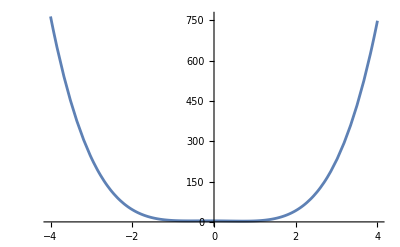

```mathematica
f1_graph=Plot[f1[x],{x,-4,4}]
```

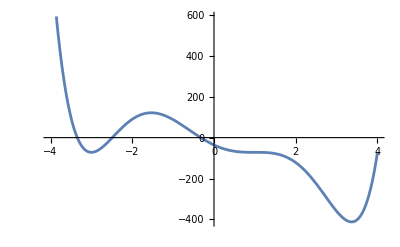

Plot::pllim: Range specification tab1 is not of the form {x, xmin, xmax}.

```mathematica
f2_graph=Plot[f2[x],{x,-4,4}]
```

{{-4.,764.669},{-3.5,445.417},{-3.,237.925},{-2.5,113.005},{-2.,45.6693},{-1.5,15.1876},{-1.,5.20151},{-0.5,3.86831},{0.,4.},{0.5,3.1612},{1.,3.70151},{1.5,12.7128},{2.,41.9193},{2.5,107.525},{3.,230.05},{3.5,434.192},{4.,748.732}}

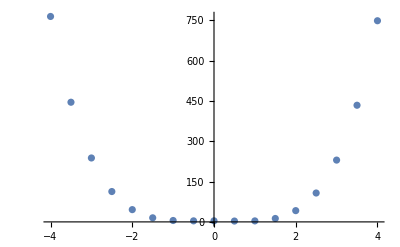

-Graphics-

-Graphics-

```mathematica
tab2 = Table[{x,f1[x]},{x,-4,4,0.5}]//N
ListPlot[tab2, PlotRange->All]
```

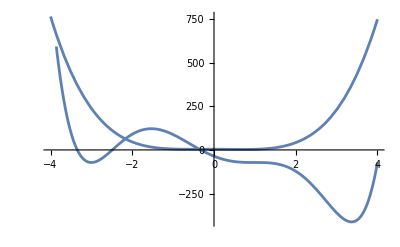

```mathematica
Show[f1graph,f2graph,PlotRange->All]
```

```mathematica
Plot3D[g[x,y],{x,-1,1},{y,4,3}]
```

-Graphics3D-

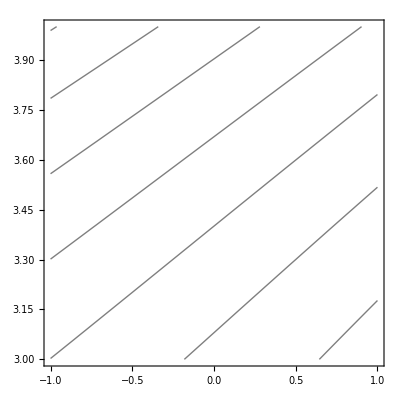

```mathematica
ContourPlot[g[x,y],{x,-1,1},{y,3,4},ContourShading->False]
```

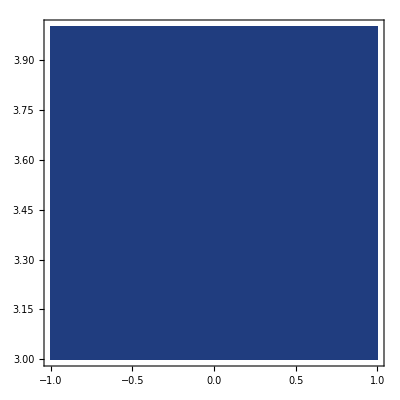

```mathematica
ContourPlot[g[x,y],{x,-1,1},{y,3,4},Contours->{0}]
```